## Problem 1.13

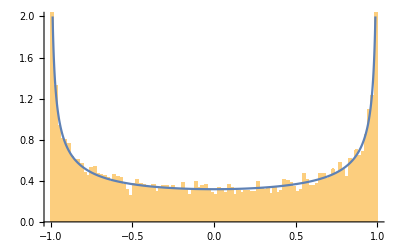

```mathematica
x[t_]:= Cos[t]
snapshots =Table[x[π RandomReal[j]],{j,10000}];
hist =Histogram[snapshots,100,"PDF",PlotRange-> {0,2}];
pl = Plot[1/(π Sin[ArcCos[x]]),{x,-1,1},PlotRange-> {0,2}];
Show[hist,pl]
```

## Problem 2.55

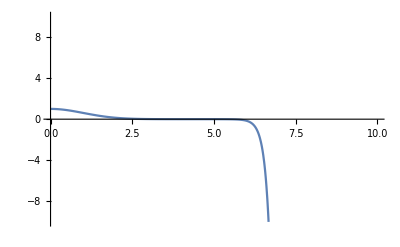

```mathematica
a = 0;
b = 10;
c=-10;
d=10;
K=1;
Plot[Evaluate[u[x] /. NDSolve[{u''[x] - (x^2-K)*u[x]==0, u[0]==1,u'[0]==0},u[x],{x,0,b}]],{x,a,b},PlotRange ->{c,d}]
```

## Problem 2.61